```mathematica
phi[x_,n_]:=(1/Pi) *(1/n)*1/(x^2+(1/n)^2)
```

10

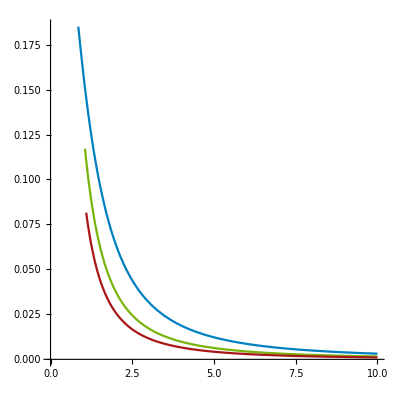

```mathematica
maxX=10
Show[
Plot[phi[x,1],{x,0,maxX},PlotStyle->{RGBColor[0, 0.501961, 0.752941]},AspectRatio->1,AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}},LabelStyle->(FontFamily->"STIX Two Text")],
Plot[phi[x,2],{x,0,maxX},PlotStyle->{RGBColor[0.47451, 0.705882, 0.0470588]},AspectRatio->1,AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}],
Plot[phi[x,3],{x,0,maxX},PlotStyle->{RGBColor[0.662745, 0.0862745, 0.0862745]},AspectRatio->1,AxesStyle->{{Arrowheads[0.02],Directive[Black]},{Arrowheads[0.02],Directive[Black]}}]
]
```